```mathematica
m=1;
v=1;
ρ=1;
α=1;
L=m*ρ*v
Ee=1/2*m*v^2-0.7
p=L^2/(m*α)
e:=Sqrt[1+(2*Ee*L^2)/(m*α^2)];
```

1

-0.2

1

```mathematica
Export["~/Dokumentumok/palyak.pdf",PolarPlot[{p/(1-e*Cos[ϕ])},{ϕ,0,2Pi},PlotRange->{{-3,5},{-3.5,3.5}},PlotStyle->{Thick}]]
```

~/Dokumentumok/palyak.pdf

```mathematica
Export["~/Dokumentumok/palyak1.eps",Show[PolarPlot[{p/(1-Sqrt[1+(2*(-0.5)*L^2)/(m*α^2)]*Cos[ϕ]),p/(1-Sqrt[1+(2*(-0.4)*L^2)/(m*α^2)]*Cos[ϕ]),p/(1-Sqrt[1+(2*0*L^2)/(m*α^2)]*Cos[ϕ])},{ϕ,0,2Pi},PlotRange->{{-1.5,5},{-3,3}},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green}}],PolarPlot[{p/(1-Sqrt[1+(2*(0.5)*L^2)/(m*α^2)]*Cos[ϕ])},{ϕ,Pi/2-ArcCos[1/(Sqrt[1+(2*(0.5)*L^2)/(m*α^2)])]+0.001,3*Pi/2+ArcCos[1/(Sqrt[1+(2*(0.5)*L^2)/(m*α^2)])]},PlotRange->{{-1.5,5},{-3,3}},PlotStyle->{Thick,Black}]]]
```

~/Dokumentumok/palyak1.eps

```mathematica
Show[PolarPlot[{p/(1+e*Cos[ϕ])},{ϕ,Pi-ArcCos[1/e],Pi+ArcCos[1/e]},PlotRange->5],PolarPlot[{p/(1+e*Cos[ϕ])},{ϕ,-Pi/2-ArcCos[1/e],Pi/2+ArcCos[1/e]},PlotRange->5]]
Show[PolarPlot[{-p/(-1+e*Cos[ϕ])},{ϕ,ArcCos[1/e],-ArcCos[1/e]},PlotRange->5],PolarPlot[{-p/(-1+e*Cos[ϕ])},{ϕ,Pi/2-ArcCos[1/e],3*Pi/2+ArcCos[1/e]},PlotRange->5]]
```

```mathematica
V[r_]:=L^2/2/m/r^2-α/r;
```

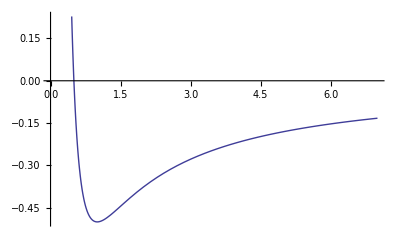

```mathematica
Plot[V[r],{r,0,7}]
```